```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Johnson.csv","HeaderLines"->1];
data2=Import["Hale.csv","HeaderLines"->1];
eps2 = Function[x,{(2*Pi)/x[[1]],(x[[2]]+I*x[[3]])^2}]/@data;
epsnew =Function[x,{(2*Pi)/x[[4]],(x[[2]]+I*x[[3]])^2}]/@data2;

eps =Interpolation[eps2];
epsf = Interpolation[Reverse[epsnew]];
```

```mathematica
P[x_,z_,kt_,delta_,k_]:=Module[{e2=x,
k0=k,
e1=1.5^2,
e3=z,
d=delta},
  kz[e_,kv_]:=Sqrt[k0^2 *e-kv ^2];


P1=({{(kz[e2,kt]/(e2*k0)+kz[e1,kt]/(e1*k0)),(kz[e2,kt]/(e2*k0)-kz[e1,kt]/(e1*k0))},{(kz[e2,kt]/(e2*k0)-kz[e1,kt]/(e1*k0)),(kz[e2,kt]/(e2*k0)+kz[e1,kt]/(e1*k0))}})/(2*kz[e2,kt]/(e2*k0));
P2=({{(kz[e3,kt]/(e3*k0)+kz[e2,kt]/(e2*k0)),(kz[e3,kt]/(e3*k0)-kz[e2,kt]/(e2*k0))},{(kz[e3,kt]/(e3*k0)-kz[e2,kt]/(e2*k0)),(kz[e3,kt]/(e3*k0)+kz[e2,kt]/(e2*k0))}}/(2*kz[e3,kt]/(e3*k0)));



J =  {{Exp[I*kz[e2,kt]*d],0},{0,Exp[-I*kz[e2,kt]*d]}};
r/.Solve[P2.J.P1.{1,r}=={t,0},{r,t}][[1]]
]
```

```mathematica
TM[x_,z_,kt_,delta_,k_]:=Module[{e2=x,
k0=k,
e1=1.5^2,
e3=z,
d=delta},
  kz[e_,kv_]:=Sqrt[k0^2 *e-kv ^2];


P1=({{(kz[e2,kt]/(e2*k0)+kz[e1,kt]/(e1*k0)),(kz[e2,kt]/(e2*k0)-kz[e1,kt]/(e1*k0))},{(kz[e2,kt]/(e2*k0)-kz[e1,kt]/(e1*k0)),(kz[e2,kt]/(e2*k0)+kz[e1,kt]/(e1*k0))}})/(2*kz[e2,kt]/(e2*k0));
P2=({{(kz[e3,kt]/(e3*k0)+kz[e2,kt]/(e2*k0)),(kz[e3,kt]/(e3*k0)-kz[e2,kt]/(e2*k0))},{(kz[e3,kt]/(e3*k0)-kz[e2,kt]/(e2*k0)),(kz[e3,kt]/(e3*k0)+kz[e2,kt]/(e2*k0))}}/(2*kz[e3,kt]/(e3*k0)));



J =  {{Exp[I*kz[e2,kt]*d],0},{0,Exp[-I*kz[e2,kt]*d]}};
P2.J.P1
]
```

```mathematica
λ1 = 650*10^-9;
λ2 = 1550*10^-9;
k1 = (2*Pi)/λ1;
k2 = (2*Pi)/λ2;
disp[k0_,kx_]:=TM[eps[k0],epsf[k0],kx,55 10^-9,k0]⟦2,2⟧(* 𝕋E[k0,kx]⟦2,2⟧*);
```

```mathematica
(* Newton Method *)
Newton[F_,K0_]:=Module[{st,k1,F1,k2,dF,j},
st=10^-9;
k1=K0;
F1=F[k1];
k2=2 k1;
dF=(F[k1+st k1]-F[k1])/(st k1);
j=0;
While[Abs[(k2-k1)/k2]>10^-5,
j++;
k2=k1;
k1=k2-F1/dF;
F1=F[k1];
dF=(F[k1+st]-F[k1])/st;
If[j>10,Print["hangup"];Break[]];
];k1];

Newton[F_,θ0_,φ0_]:=Module[{st,θ1,φ1,F1,θ2,φ2,dFθ,dFφ,j},
st=10^-8;
θ1=θ0;φ1=φ0;
F1=F[θ1,φ1];
θ2=θ1+π;φ2=φ1+π;
dFθ=(F[θ1+st,φ1]-F1)/st;dFφ=(F[θ1,φ1+st]-F1)/st;
j=0;
While[Abs[θ2-θ1]>10^-3 π&&Abs[φ2-φ1]>10^-3 π,
j++;
θ2=θ1;φ2=φ1;
θ1=θ2-Im[dFφ* F1]/Im[dFφ* dFθ];φ1=φ2-Im[dFθ* F1]/Im[dFθ* dFφ];
F1=F[θ1,φ1];
(*Print[θ1,"   ",φ1,"   ",F1];*)
dFθ=(F[θ1+st,φ1]-F1)/st;dFφ=(F[θ1,φ1+st]-F1)/st;
If[j>200,(*Print["hangup"];*)Break[]];
];(*Print[F1];*){θ1,φ1}];
(*wD=k0/.FindRoot[Re[ϵAg[k0]]==-Re@ϵD[k0],{k0,12}];
wQ=k0/.FindRoot[Re[ϵAg[k0]]==-ϵQ,{k0,16}];*)

kmax=∞; (* ограничение области волновых чисел для построения дисперсии *)

FindDispersion:=Module[{},
α=1;
FE[θ_,φ_,k0_,k_,Δ_]:=disp[k0+Δ Cos[θ],k+Δ Sin[θ] Exp[ⅈ φ]];
Clear[Disp];
nxt=0;(* переменная для ручной остановки движения по кривой *)
For[jj=1,jj≤Length[KStart],jj++,

kk=KStart⟦jj,1⟧+ⅈ 10^-5;
sq[z_]:=If[Arg[z]>-π/2,√z,-√z];
(* плавное включение потерь *)
(*Do[(* здесь γ -- локальная переменная, растущая от 0 до внешнего значения γ *)
kk=Newton[disp[KStart⟦jj,2⟧,#]&,kk],
{γ,0,γ,γ/10}];*)
kk=Newton[disp[KStart⟦jj,2⟧,#]&,kk];
Disp[jj]={{KStart⟦jj,2⟧,kk}};

{Θi,Φi}={Θ1,Φ1}=Newton[FE[#1,#2,Disp[jj]⟦-1,1⟧,Disp[jj]⟦-1,2⟧,Δ0/100]&,1.5,0.01];
(* поскольку направление движения неизвестно, первый шаг надо делать очень маленьким *)
(*Print[DensityPlot[Log@Abs@FE[θ,φ,Disp[jj]⟦-1,1⟧,Disp[jj]⟦-1,2⟧,Δ0/100],{θ,0,π},{φ,-π,π},FrameLabel->{"θ","φ"},AxesOrigin->{0,0},Epilog->{Red,Point[{Θ1,Φ1}]}]];*)
(*Return[];*)

AppendTo[Disp[jj],
{Disp[jj]⟦-1,1⟧+Δ0/100 Cos[Θi],Disp[jj]⟦-1,2⟧+Δ0/100 Sin[Θi] Exp[ⅈ Φi]}
]; (* {Θi,Φi} ниже используется, чтобы пойти обратно по кривой *)

While[(Re[Disp[jj]⟦-1,2⟧]/Disp[jj]⟦-1,1⟧<kmax)&&(Re[Disp[jj]⟦-1,1⟧]<k0max)&&(Re[Disp[jj]⟦-1,1⟧]>k0min)&&(Re[Disp[jj]⟦-1,2⟧]>0),
If[nxt==1,nxt=0;Break[]];
{Θ0,Φ0}={Θ1,Φ1};
inc=0;
Label[1];
sq[z_]:=If[Arg[z]>-α π/2,√z,-√z];
{Θ1,Φ1}=Newton[FE[#1,#2,Disp[jj]⟦-1,1⟧,Disp[jj]⟦-1,2⟧,Δ0]&,Θ0,Φ0];
(*Print[DensityPlot[Log@Abs@FE[θ,φ,Disp[jj]⟦-1,1⟧,Disp[jj]⟦-1,2⟧,Δ0/100],{θ,0,π},{φ,-π,π},FrameLabel->{"θ","φ"},AxesOrigin->{0,0},Epilog->{Red,Point[{Θ1,Φ1}]}]];
Print[{Θ1,Φ1}];*)
(*Return[];*)
F1=FE[Θ1,Φ1,Disp[jj]⟦-1,1⟧,Disp[jj]⟦-1,2⟧,Δ0];
sq[z_]:=-If[Arg[z]>-α π/2,√z,-√z];(* вычисление дисперсии с другой веткой √□ *)
{Θ2,Φ2}=Newton[FE[#1,#2,Disp[jj]⟦-1,1⟧,Disp[jj]⟦-1,2⟧,Δ0]&,Θ0,Φ0];
F2=FE[Θ2,Φ2,Disp[jj]⟦-1,1⟧,Disp[jj]⟦-1,2⟧,Δ0];
sq[z_]:=If[Arg[z]>-α π/2,√z,-√z];(* восстановление исходной ветви корня *)

Module[{
n0={Sin[Θ0] Cos[Φ0],Sin[Θ0] Sin[Φ0],Cos[Θ0]},n1={Sin[Θ1] Cos[Φ1],Sin[Θ1] Sin[Φ1],Cos[Θ1]},n2={Sin[Θ2] Cos[Φ2],Sin[Θ2] Sin[Φ2],Cos[Θ2]}
},
If[Abs[n2.n0-1]>0.01&&Abs[n1.n0-1]>0.01,
α=α/2;
inc++;If[inc≥3,α=1;Print["Jump detected, aborting"];Goto[2]];(* аварийный выход из цикла *)
Goto[1](* если обе касательные к дисперсии изменились более, чем на 0.01, подвинуть разрез путем изменения α *)
];
α=1;
Which[Abs[F1]>10^2 Abs[F2],{Θ1,Φ1}={Θ2,Φ2},
Abs[F2]>10^2 Abs[F1],{Θ1,Φ1}={Θ1,Φ1},(* если одна из двух точек минимизирует функцию намного лучше, использовать её *)
n2.n0>n1.n0,{Θ1,Φ1}={Θ2,Φ2} (* в противном случае выбрать смещение, более похоже на предыдущее *)
]
];
AppendTo[Disp[jj],
{Disp[jj]⟦-1,1⟧+Δ0 Cos[Θ1],Disp[jj]⟦-1,2⟧+Δ0 Sin[Θ1] Exp[ⅈ Φ1]}
]
];

Label[2];

nxt=0;(* переменная для ручной остановки движения по кривой *)
sq[z_]:=If[Arg[z]>-π/2,√z,-√z];{Θ1,Φ1}=Newton[FE[#1,#2,Disp[jj]⟦1,1⟧,Disp[jj]⟦1,2⟧,Δ0]&,π-Θi,π+Φi];
While[(Re[Disp[jj]⟦1,2⟧]/Disp[jj]⟦1,1⟧<kmax)&&(Re[Disp[jj]⟦1,1⟧]<k0max)&&(Re[Disp[jj]⟦1,1⟧]>k0min)&&(Re[Disp[jj]⟦1,2⟧]>0),
If[nxt==1,nxt=0;Break[]];
{Θ0,Φ0}={Θ1,Φ1};

inc=0;
Label[3];
sq[z_]:=If[Arg[z]>-α π/2,√z,-√z];{Θ1,Φ1}=Newton[FE[#1,#2,Disp[jj]⟦1,1⟧,Disp[jj]⟦1,2⟧,Δ0]&,Θ0,Φ0];
sq[z_]:=-If[Arg[z]>-α π/2,√z,-√z];(* вычисление дисперсии с другой веткой √□ *)
{Θ2,Φ2}=Newton[FE[#1,#2,Disp[jj]⟦1,1⟧,Disp[jj]⟦1,2⟧,Δ0]&,Θ0,Φ0];
sq[z_]:=If[Arg[z]>-α π/2,√z,-√z];
Module[
{
n0={Sin[Θ0] Cos[Φ0],Sin[Θ0] Sin[Φ0],Cos[Θ0]},n1={Sin[Θ1] Cos[Φ1],Sin[Θ1] Sin[Φ1],Cos[Θ1]},n2={Sin[Θ2] Cos[Φ2],Sin[Θ2] Sin[Φ2],Cos[Θ2]}
},
If[Abs[n2.n0-1]>0.01&&Abs[n1.n0-1]>0.01,
α=α/2;
inc++;If[inc≥3,α=1;Goto[4]];(* аварийный выход из цикла *)
Goto[3](* если обе касательные к дисперсии изменились более, чем на 0.01, подвинуть разрез путем изменения α *)
];
α=1;
Which[Abs[F1]>10^2 Abs[F2],{Θ1,Φ1}={Θ2,Φ2},
Abs[F2]>10^2 Abs[F1],{Θ1,Φ1}={Θ1,Φ1},(* если одна из двух точек минимизирует функцию намного лучше, использовать её *)
n2.n0>n1.n0,{Θ1,Φ1}={Θ2,Φ2} (* в противном случае выбрать смещение, более похоже на предыдущее *)
]];

PrependTo[Disp[jj],
{Disp[jj]⟦1,1⟧+Δ0 Cos[Θ1],Disp[jj]⟦1,2⟧+Δ0 Sin[Θ1] Exp[ⅈ Φ1]}
]
];Label[4]];jj--];
```

Epilog→{InfiniteLine[{0,0},{1,0.751315}],InfiniteLine[{0,0},{1,0.666667}]}

General::munfl: Exp[-8140.+9.89267×10^-6 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-74058.6+1.08733×10^-6 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-139977.+5.75282×10^-7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

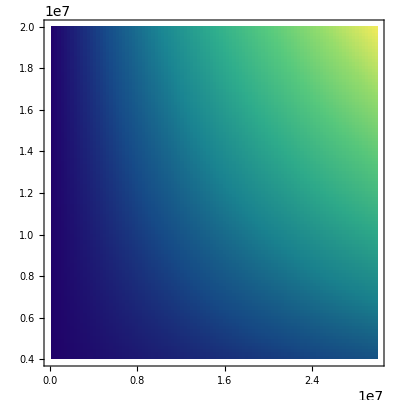

```mathematica
γ=1;
Dynamic[pr]
Q0min=0.4 10^7;Q0max=2. 10^7;nk0=100;
Kmin=37000;Kmax=3. 10^7;nk=100;
epilog=Epilog->{InfiniteLine[{0,0},{1,1/Re[√epsf[k1]]}],InfiniteLine[{0,0},{1,1/Re[1.5]}]}
DP=Table[pr=(k0-Q0min)/(Q0max-Q0min)//N;Log[Abs[disp[k0,κ k0]]^2],{k0,Q0min,Q0max,(Q0max-Q0min)/nk0},{κ,Kmin,Kmax,(Kmax-Kmin)/nk}];
dp=ReliefPlot[DP,ColorFunction->"BlueGreenYellow",PlotRange->All,(*PlotLegends->Automatic,*)AspectRatio->1,DataRange->{{Kmin,Kmax},{Q0min,Q0max}},FrameTicks->True,Epilog->epilog,ImageSize->400]
```

```mathematica
NofPoints=1;    (* число точек *)
Dynamic[KStart]
pts0=Table[{k,(Q0max+Q0min)/2},{k,Kmin+(Kmax-Kmin)/(2 NofPoints),Kmax,(Kmax-Kmin)/NofPoints}];
DynamicModule[{pts=pts0},LocatorPane[Dynamic[pts],Dynamic[Show[κStart=pts;dp]]]]
```

```mathematica
γ=1;
KStart=Table[{κStart⟦j,1⟧ κStart⟦j,2⟧,κStart⟦j,2⟧},{j,Length@κStart}];kmax=Kmax; (* ограничение области волновых чисел для построения дисперсии *)
k0max=Q0max; (* ограничение области частот для построения дисперсии *)
k0min=Q0min;
Δ0=0.01 Q0max;
th=0.005;
Cls={Red,Blue,Darker[Green],Magenta,Orange,Darker[Yellow],Purple};
FindDispersion;
(*Table[PrependTo[Disp[jjj],{0,0}],{jjj,NofPoints}]; *)(* добавление точки {0,0} *)
```

$Aborted

```mathematica
Dynamic[Column[{
Button["NextCurve",nxt=1],
Column[{
Row[{
ListPlot[Table[{Re@Disp[jjj]⟦l,2⟧,Disp[jjj]⟦l,1⟧},{jjj,jj},{l,Length[Disp[jjj]]}],
BaseStyle->{12,FontFamily->"Times"},Frame->True,FrameLabel->{"Re k","k_0"},AspectRatio->0.7,PlotRange->All,PlotStyle->Table[{col,Thickness[th]},{col,Cls}],Epilog->{InfiniteLine[{{0,0},{√(Re@ϵV[2π/λ0]),1}}],InfiniteLine[{{0,0},{√(Re@ϵD[2π/λ0]),1}}]},GridLines->{{0},{0,2π/λ0}},AxesOrigin->{0,0},ImageSize->300],
ListPlot[Table[{Re@Disp[jjj]⟦l,2⟧/Disp[jjj]⟦l,1⟧,Disp[jjj]⟦l,1⟧},{jjj,jj},{l,Length[Disp[jjj]]}],
BaseStyle->{12,FontFamily->"Times"},Frame->True,FrameLabel->{"Re k/k_0","k_0"},AspectRatio->0.7,PlotRange->All,PlotStyle->Table[{col,Thickness[th]},{col,Cls}],Epilog->epilog,GridLines->{{0},{0,2π/λ0}},AxesOrigin->{0,0},ImageSize->300]
}],
ListPlot[Table[{Im@Disp[jjj]⟦l,2⟧,Disp[jjj]⟦l,1⟧},{jjj,jj},{l,Length[Disp[jjj]]}],
BaseStyle->{12,FontFamily->"Times"},Frame->True,FrameLabel->{"Im k","k_0"},AspectRatio->0.7,(*PlotRange->All,*)PlotStyle->Table[{col,Thickness[th]},{col,Cls}],GridLines->{{0},{0,2π/λ0}},Axes->None,(*AxesOrigin->{0,0},*)ImageSize->300]
}]}]]
```

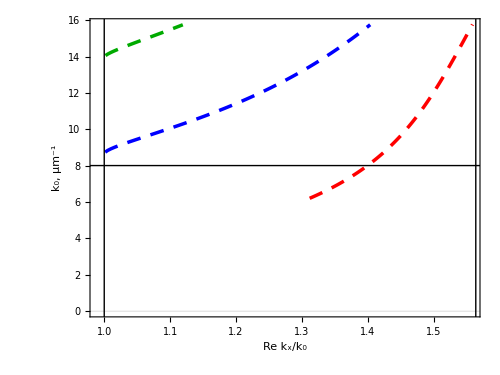

```mathematica
TERek=ListPlot[Table[{Re[Disp[jj]⟦l,2⟧]/(Disp[jj]⟦l,1⟧),Disp[jj]⟦l,1⟧},{jj,Length[KStart]},{l,Length[Disp[jj]]}],
Frame->True,FrameLabel->{{"k_0, μm^-1"," λ,nm"},{"Re k_x/k_0",""}},FrameTicks->{{Automatic,Table[{2π 10^3/l,l},{l,{500,600,700,800,900,1000}}]},{Automatic,Table[{2π 10^3/l,l},{l,{150,200,300,400,600,900,2000}}]}},AspectRatio->0.75,PlotRange->All,PlotStyle->Table[{col,Thickness[th],Dashing[{0.02,0.015}]},{col,Cls}],Epilog->epilog,GridLines->{{0},{0,2π/λ0}},Joined->True,InterpolationOrder->1,BaseStyle->{FontFamily->"Times",16},ImageSize->500,LabelStyle->Black]
```

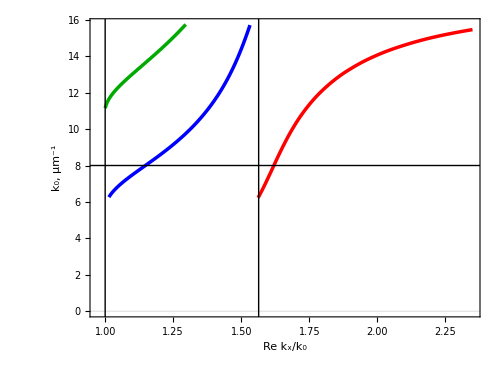

```mathematica
TMRek=ListPlot[Table[{Re[Disp[jj]⟦l,2⟧]/(Disp[jj]⟦l,1⟧),Disp[jj]⟦l,1⟧},{jj,Length[KStart]},{l,Length[Disp[jj]]}],
Frame->True,FrameLabel->{{"k_0, μm^-1"," λ,nm"},{"Re k_x/k_0",""}},FrameTicks->{{Automatic,Table[{2π 10^3/l,l},{l,{500,600,700,800,900,1000}}]},{Automatic,Table[{2π 10^3/l,l},{l,{150,200,300,400,600,900,2000}}]}},AspectRatio->0.75,PlotRange->All,PlotStyle->Table[{col,Thickness[th]},{col,Cls}],Epilog->epilog,GridLines->{{0},{0,2π/λ0}},Joined->True,InterpolationOrder->1,BaseStyle->{FontFamily->"Times",16},ImageSize->500,LabelStyle->Black]
```

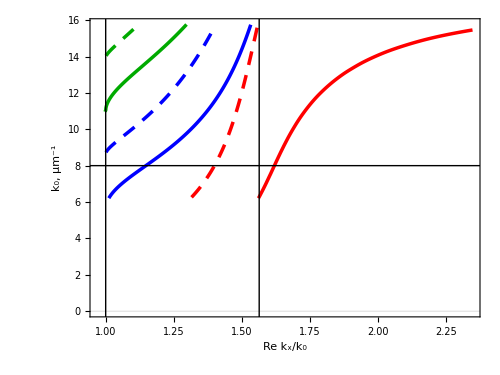

```mathematica
Show[{TMRek,TERek}]
```

```mathematica
Put[Table[{Re[Disp[jj]⟦l,2⟧],Disp[jj]⟦l,1⟧},{jj,Length[KStart]},{l,Length[Disp[jj]]}],"Ag#SU8#V PlanarDispTE.dat"]
```

```mathematica
Table[Export["Ag#SU8#V lambda vs n_eff TM Mode N"<>ToString[jj]<>".dat",Sort[{1000 2π/Disp[jj]⟦All,1⟧,Re[Disp[jj]⟦All,2⟧]/Disp[jj]⟦All,1⟧}ᵀ]],{jj,Length[KStart]}]
```

{Ag#SU8#V lambda vs n_eff TM Mode N1.dat,Ag#SU8#V lambda vs n_eff TM Mode N2.dat,Ag#SU8#V lambda vs n_eff TM Mode N3.dat}

```mathematica
(* РАСЧЕТ ПОЛЯ *)
```

```mathematica
(*основные функции*)
dM=0.1;
edArrayt2[k0_]:={{ϵSub[k0],0.1},{ϵD[k0],dD}};

SetDirectory[NotebookDirectory[]];
(*<<"eAuRakic.txt"*)
eext=ϵV[2π/λ0];
eext2=ϵV[2π/λ0];

J[k1_]:=({{Exp[I*k1], 0}, {0, Exp[-I*k1]}});

S[z1_,z2_]:=({{(z2+z1)/(2*z2), (z2-z1)/(2*z2)}, {(z2-z1)/(2*z2), (z2+z1)/(2*z2)}});
kz2[e_,k0_,kx_]:=sq[k0*k0*e-kx^2];
zE[e_,k0_,kx_]:=kz2[e,k0,kx]/(k0);
zM[e_,k0_,kx_]:=kz2[e,k0,kx]/(k0 e);
sq[z_]:=If[Arg[z]<-0.8π,-√z,√z];
Ttot[edarrayt_,k0_,kx_]:=Module[{j,kzs,temp,Tc,n},
Tc={{1,0},{0,1}};
n=Length[edarrayt];
For[j=1,j≤Length[edarrayt],j++,
(*волновые числа и импедансы в слоях:*)
kzs=edarrayt⟦j,2⟧sq[k0^2 edarrayt⟦j,1⟧-kx^2];
(*Т-матрица ячейки cлучай промежуточных слоев*);
If[j≠1,temp=J[kzs].S[zM[edarrayt⟦j-1,1⟧,k0,kx],zM[edarrayt⟦j,1⟧,k0,kx]].Tc,
temp=J[kzs].S[zM[eext,k0,kx],zM[edarrayt⟦j,1⟧,k0,kx]].Tc;
];
(*обновление всей матрицы*);
Tc=temp;
];
temp=S[zM[edarrayt⟦Length[edarrayt],1⟧,k0,kx],zM[eext2,k0,kx]].Tc;
temp
];(*endmod*)

 (*2*)(*коэффициент отражения*)
r[edarrayt_,k0_,kx_]:=-(Ttot[edarrayt,k0,kx]⟦2,1⟧)/(Ttot[edarrayt,k0,kx]⟦2,2⟧);
t[edarrayt_,k0_,kx_]:=-(Det[Ttot[edarrayt,k0,kx]](*(√□)*))/(Ttot[edarrayt,k0,kx]⟦2,2⟧);
 
 (*4*)(*функция нахождения номера слоя в зависимости от координаты*)
nl[edarrayt_,z_]:=Module[{j,n},
If[z≤0,n=0,
For[j=2,j≤Length[edarrayt],j++,
If[Sum[edarrayt⟦i,2⟧,{i,1,j-1}]≤z≤Sum[edarrayt⟦i,2⟧,{i,1,j}],n=j];
];
];
If[0≤z≤edarrayt⟦1,2⟧,n=1];
If[Sum[edarrayt⟦i,2⟧,{i,1,Length[edarrayt]}]≤z,n=-1];
n
];(*endmod*)

 (*5*)(*функция вычисления Т-матрицы в произвольном слое (внутри кристалла)*)
T[edarrayt_,k0_,kx_,z_]:=Module[{j,n,rtot,TTemp,kzs,Tc},
Tc={{1,0},{0,1}};
n=nl[edarrayt,z];
If[n>0,
For[j=1,j≤n,j++,
(*волновые числа и импедансы в слоях:*)
If[j<n,
kzs=edarrayt⟦j,2⟧sq[k0^2 edarrayt⟦j,1⟧-kx^2],
If[n>1,kzs=(z-Sum[edarrayt⟦i,2⟧,{i,1,n-1}])sq[k0^2 edarrayt⟦j,1⟧-kx^2],kzs=z sq[k0^2 edarrayt⟦j,1⟧-kx^2]];
];(*варианты, когда z в первом слое, когда рассматривается слой в котором находится конечное значение z и в котором не находится*)

(*Т-матрица ячейки cлучай промежуточных слоев*)
If[j≠1,TTemp=J[kzs].S[zM[edarrayt⟦j-1,1⟧,k0,kx],zM[edarrayt⟦j,1⟧,k0,kx]].Tc,
TTemp=J[kzs].S[zM[eext,k0,kx],zM[edarrayt⟦j,1⟧,k0,kx]].Tc;
];
(*обновление всей матрицы*)
Tc=TTemp;
(*If[Mod[j1,100]==1,Print[Norm[Tc]]];*)
],Tc=J[(z-Sum[edarrayt⟦i,2⟧,{i,1,Length[edarrayt]}])sq[k0^2-kx^2]].Ttot[edarrayt,k0,kx];
];
Tc
];(*endmod*)

 (*6*)(*функция вычисления поля в произвольном z*)
H[edarrayt_,k0_,kx_,z_]:=Module[{n},
n=nl[edarrayt,z];
Which[n>0,T[edarrayt,k0,kx,z].{1 ,r [edarrayt,k0,kx]},n==0,J[sq[k0^2-kx^2] z].{1 ,r [edarrayt,k0,kx]},n==-1,J[(z-Sum[edarrayt⟦i,2⟧,{i,1,Length[edarrayt]}])sq[k0^2-kx^2]].Ttot[edarrayt,k0,kx].{1 ,r [edarrayt,k0,kx]}]
];(*endmod*)

HEig[edarrayt_,k0_,kx_,z_]:=Module[{n},
n=nl[edarrayt,z];
Which[n>0,T[edarrayt,k0,kx,z].{0 ,1},
n==0,J[sq[eext k0^2-kx^2] z].{0 ,1},
n==-1,J[(z-Sum[edarrayt⟦i,2⟧,{i,1,Length[edarrayt]}]) sq[k0^2 eext2-kx^2]].Ttot[edarrayt,k0,kx].{0 ,1}]
];(*endmod*)
```

```mathematica
LocatorPane[Dynamic[pts],Show[KStart=pts;dp,ImageSize->300](*,ContinuousAction->False*)](*,
Dynamic[ListPlot[Table[{z,Abs[H[edArrayt2[pts⟦2⟧],pts⟦2⟧,pts⟦1⟧,z]⟦1⟧+H[edArrayt2[pts⟦2⟧],pts⟦2⟧,pts⟦1⟧,z]⟦2⟧]^2},{z,-0.1,Sum[edArrayt2[pts⟦2⟧]⟦i,2⟧,{i,1,Length[edArrayt2[pts⟦2⟧]]}]+0.3Sum[edArrayt2[pts⟦2⟧]⟦i,2⟧,{i,1,Length[edArrayt2[pts⟦2⟧]]}],0.002}],Joined->True,PlotRange->All,ImageSize->300,GridLines->{Table[Total@Take[edArrayt2[k0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[k0]ᵀ⟦2⟧]}],None}]]*)
Dynamic[pts]
```

```mathematica
(* мода в месте расположения точки *)
K0=pts⟦2⟧;
Kx=FindRoot[disp[K0,kx],{kx,K0 pts⟦1⟧}(*,MaxIterations->∞,WorkingPrecision->20*)(*,Method->"Secant"*)]⟦1,2⟧;
Print["k_x/k_0=",Kx/K0]
Print["k_x'/k_x''=",Re[Kx]/Im[Kx]]
```

k_x/k_0=1.65467+0.00240271 ⅈ

k_x'/k_x''=688.666

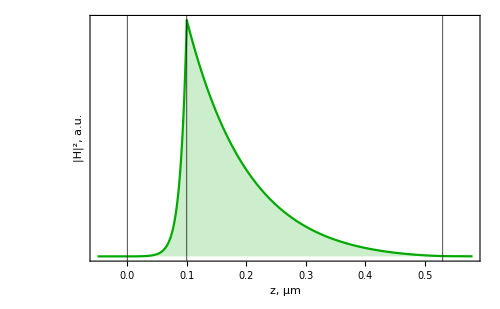

```mathematica
ListPlot[Table[{z,Abs[Total@HEig[edArrayt2[K0],K0,Kx,z]]^2},{z,-0.05,Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}]+0.05,0.001}],Axes->None,Joined->True,PlotRange->{0,All},ImageSize->500,GridLinesStyle->Directive[Black],GridLines->{{0}~Join~Table[Total@Take[edArrayt2[K0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[K0]ᵀ⟦2⟧]}],None},Frame->True,FrameLabel->{"z, μm","|H|^2, a.u."},BaseStyle->{FontFamily->"Times",16},FrameStyle->Black,FrameTicks->{Automatic,None},PlotStyle->Darker@Green,Filling->Axis]
```

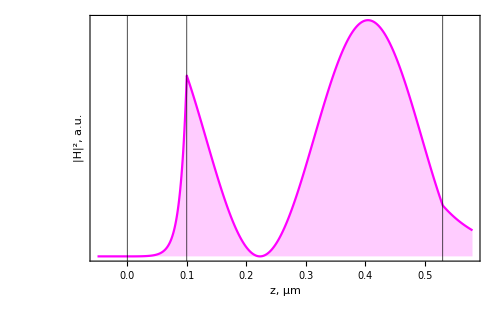

```mathematica
ListPlot[Table[{z,Abs[Total@HEig[edArrayt2[K0],K0,Kx,z]]^2},{z,-0.05,Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}]+0.05,0.001}],Axes->None,Joined->True,PlotRange->{0,All},ImageSize->500,GridLinesStyle->Directive[Black],GridLines->{{0}~Join~Table[Total@Take[edArrayt2[K0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[K0]ᵀ⟦2⟧]}],None},Frame->True,FrameLabel->{"z, μm","|H|^2, a.u."},BaseStyle->{FontFamily->"Times",16},FrameStyle->Black,FrameTicks->{Automatic,None},PlotStyle->Magenta(*Darker@Green*),Filling->Axis]
```

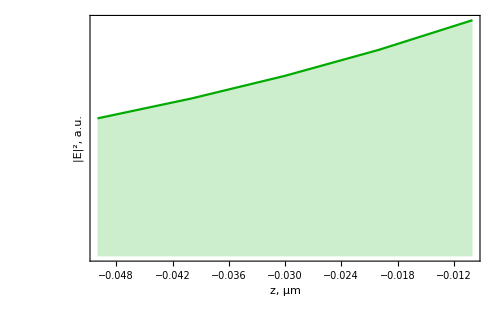

```mathematica
ListPlot[Table[{z,Abs[Total@HEig[edArrayt2[K0],K0,Kx,z]]^2},{z,-0.05,Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}]+0.05,0.01}],Axes->None,Joined->True,PlotRange->{0,All},ImageSize->500,GridLinesStyle->Directive[Black],GridLines->{{0}~Join~Table[Total@Take[edArrayt2[K0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[K0]ᵀ⟦2⟧]}],None},Frame->True,FrameLabel->{"z, μm","|E|^2, a.u."},BaseStyle->{FontFamily->"Times",16},FrameStyle->Black,FrameTicks->{Automatic,None},PlotStyle->Darker@Green,Filling->Axis]
```

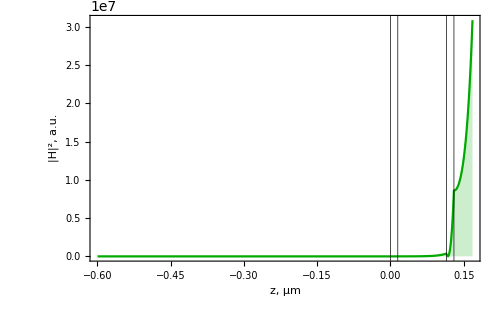

```mathematica
(*k0=pts⟦2⟧;*)
K0=k0;
(*Kx=FindRoot[disp[pts⟦2⟧,kx],{kx,pts⟦1⟧}]⟦1,2⟧*)
ListPlot[Table[{z,Abs[Total@HEig[edArrayt2[K0],K0,Kx,z]]^2},{z,-0.6,Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}]+0.3Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}],0.002}],Axes->None,Joined->True,PlotRange->{0,All},ImageSize->500,GridLinesStyle->Directive[Black],GridLines->{{0}~Join~Table[Total@Take[edArrayt2[k0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[k0]ᵀ⟦2⟧]}],None},Frame->True,FrameLabel->{"z, μm","|H|^2, a.u."},BaseStyle->{FontFamily->"Times",16},FrameStyle->Black,PlotStyle->Darker@Green,Filling->Axis]
```

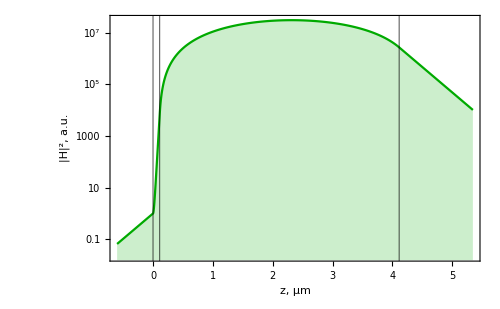

```mathematica
ListLogPlot[Table[{z,Abs[Total@HEig[edArrayt2[K0],K0,Kx,z]]^2},{z,-0.6,Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}]+0.3Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}],0.002}],Axes->None,Joined->True,PlotRange->All,ImageSize->500,GridLinesStyle->Directive[Black],GridLines->{{0}~Join~Table[Total@Take[edArrayt2[K0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[K0]ᵀ⟦2⟧]}],None},Frame->True,FrameLabel->{"z, μm","|H|^2, a.u."},BaseStyle->{FontFamily->"Times",16},FrameStyle->Black,PlotStyle->Darker@Green,Filling->Axis]
```

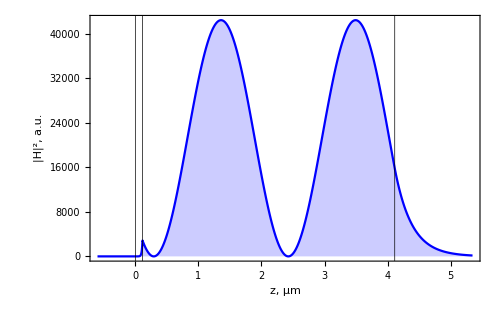

```mathematica
(*k0=pts⟦2⟧;*)
K0=k0;
(*Kx=FindRoot[disp[pts⟦2⟧,kx],{kx,pts⟦1⟧}]⟦1,2⟧*)
ListPlot[Table[{z,Abs[Total@HEig[edArrayt2[K0],K0,Kx,z]]^2},{z,-0.6,Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}]+0.3Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}],0.002}],Axes->None,Joined->True,PlotRange->{0,All},ImageSize->500,GridLinesStyle->Directive[Black],GridLines->{{0}~Join~Table[Total@Take[edArrayt2[k0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[k0]ᵀ⟦2⟧]}],None},Frame->True,FrameLabel->{"z, μm","|H|^2, a.u."},BaseStyle->{FontFamily->"Times",16},FrameStyle->Black,PlotStyle->Blue,Filling->Axis]
```

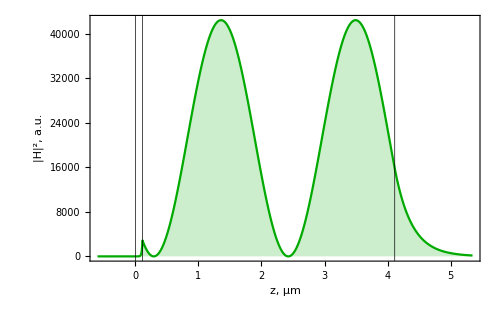

$Aborted

```mathematica
(*k0=pts⟦2⟧;*)
K0=k0;
(*Kx=FindRoot[disp[pts⟦2⟧,kx],{kx,pts⟦1⟧}]⟦1,2⟧*)
ListPlot[Table[{z,Abs[Total@HEig[edArrayt2[K0],K0,Kx,z]]^2},{z,-0.6,Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}]+0.3Sum[edArrayt2[K0]⟦i,2⟧,{i,1,Length[edArrayt2[K0]]}],0.002}],Axes->None,Joined->True,PlotRange->{0,All},ImageSize->500,GridLinesStyle->Directive[Black],GridLines->{{0}~Join~Table[Total@Take[edArrayt2[k0]ᵀ⟦2⟧,j],{j,Length[edArrayt2[k0]ᵀ⟦2⟧]}],None},Frame->True,FrameLabel->{"z, μm","|H|^2, a.u."},BaseStyle->{FontFamily->"Times",16},FrameStyle->Black,PlotStyle->Darker@Green,Filling->Axis]
```